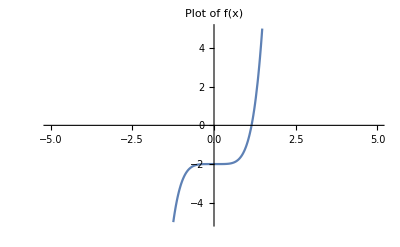

```mathematica
Plot[x^5-2,{x,-5,5},PlotRange->{-5,5},PlotLabel->"Plot of f(x)"]
```

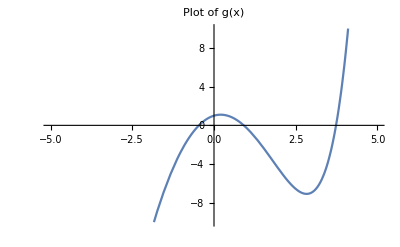

```mathematica
Plot[E^x-3x^2,{x,-5,5},PlotRange->{-10,10},PlotLabel->"Plot of g(x)"]
```

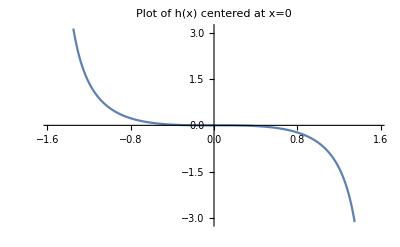

```mathematica
Plot[x-Tan[x],{x,-Pi/2,Pi/2},PlotRange->{-Pi,Pi},PlotLabel->"Plot of h(x) centered at x=0"]
```

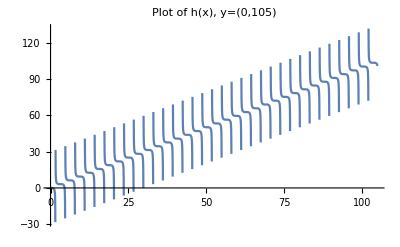

```mathematica
Plot[x-Tan[x],{x,0,105},PlotRange->Automatic,PlotLabel->"Plot of h(x), y=(0,105)"]
```

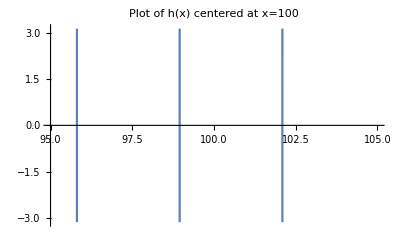

```mathematica
Plot[x-Tan[x],{x,95,105},PlotRange->{-Pi,Pi},PlotLabel->"Plot of h(x) centered at x=100"]
```

```mathematica
NumberForm[Solve[x^5-2==0,x],16]
```

{{x→-(-2)^(1/5)},{x→2^(1/5)},{x→(-1)^(2/5) 2^(1/5)},{x→-(-1)^(3/5) 2^(1/5)},{x→(-1)^(4/5) 2^(1/5)}}

```mathematica
N[{{x->-(-2)^(1/5)},{x->2^(1/5)},{x->(-1)^(2/5) 2^(1/5)},{x->-(-1)^(3/5) 2^(1/5)},{x->(-1)^(4/5) 2^(1/5)}}]
```

{{x→-0.929316-0.675188 ⅈ},{x→1.1487},{x→0.354967+1.09248 ⅈ},{x→0.354967-1.09248 ⅈ},{x→-0.929316+0.675188 ⅈ}}

```mathematica
NumberForm[Solve[E^x-3*x^2==0,x],16]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-2 ProductLog[-1/(2 √3)]},{x→-2 ProductLog[1/(2 √3)]},{x→-2 ProductLog[-1,-1/(2 √3)]}}

```mathematica
N[{{x->-2 ProductLog[-1/(2 √3)]},{x->-2 ProductLog[1/(2 √3)]},{x->-2 ProductLog[-1,-1/(2 √3)]}}]
```

{{x→0.910008},{x→-0.458962},{x→3.73308}}

```mathematica
x/.{{x->0.9100075724887093},{x->-0.4589622675369486},{x->3.733079028632814}}
```

{0.910008,-0.458962,3.73308}

```mathematica
Transpose[{{x->0.9100075724887093},{x->-0.4589622675369486},{x->3.733079028632814}}]
```

{{x→0.910008,x→-0.458962,x→3.73308}}

```mathematica
NumberForm[Solve[x-Tan[x]==0,x],16]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[x-Tan[x]==0,x]